The nonlinear optical phase shift via the cascaded 2nd order nonlinearity 
Prof. Charlie Ironside
Department of Physics and Astronomy
Curtin University 
Bentley Campus,
Western Australia 6102
email: Charlie.Ironside@curtin.edu.au
web page address:http://oasisapps.curtin.edu.au/staff/profile/view/Charlie.Ironside
Included in the book : “Semiconductor Integrated Optics for Switching Light” by Charlie Ironside 

This notebook is based on :-
C. N. Ironside, J. S. Aitchison, and J. M. Arnold, “An All-Optical Switch Employing the Cascaded 2nd-Order Nonlinear Effect,” IEEE Journal of Quantum Electronics, vol. 29, pp. 2650-2654, Oct 1993  http://dx.doi.org/10.1109/3.250387
The equation numbers refer to the equations in the above paper



We model the 2nd Order nonlinear effect Cascade effect. The input parameters are the material linear and nonlinear optical characteristics and parameters related to the device dimensions.
 Material parameters:The refractive index at the fundamental frequency,ω, and second harmonic frequency 2ω, the d coefficient for second harmonic generation. 
 Device parameters: The length of waveguides (in the different arms of the interferometer) and the phase mismatch which can be traced back to the period of the phase match gratings and the difference in the refractive index for the fundamental and the second harmonic
 Operating parameters: the wavelength of the fundamental, the range of input powers

```mathematica
(*Material Parameters for GaAs*)
(*SI units employed*)

nω:=3.45; 	(* refractive index at 1.5 microns*)
n2ω:=3.6;	(* refractive indexat 750 nm*)
deff:=150×10^-12 ; 	(* Second Harmonic generation coefficient for GaAs, d14 *)
len:=0.01; (*input in m this value 1 cm*)
miss:=2.0;(* Phase missmatch= +and- miss Pi*)
bias:=0;(* Phase offset *)
(*wavelength Parameters*)
λ:=1.5 10^-6; (*Wavelength m*)
k:=2*Pi/λ(*k vector*)
Δn:=n2ω-nω
Λ=(2λ)/(4Δn-miss λ)
Print["Grating period= ",Λ, "m"]
```

5.00003×10^-6

Grating period= 5.00003×10^-6m

SetDelayed::wrsym: Symbol Padding is Protected.

$Failed

Plot::exclul: {((1-√(1+Times[«2»])+7.03867×10^-7 Irrad) Sin[Phase]^2)/(1+√(1+Times[«2»])+7.03867×10^-7 Irrad)-1,(1-(1.42072×10^6 (-1+√Plus[«2»]))/Irrad) Sin[Phase]^2-1,Cos[Phase]-0,(1+1.40773×10^-6 Irrad)-0,(1+√(1+1.40773×10^-6 Irrad)+7.03867×10^-7 Irrad)-0,Irrad-0,(1+√(1+1.40773×10^-6 Irrad)+7.03867×10^-7 Irrad)-0,1.40773×10^-6 Im[Irrad]-0,Im[√(1+1.40773×10^-6 Irrad)+7.03867×10^-7 Irrad]-0} must be a list of equalities or real-valued functions.

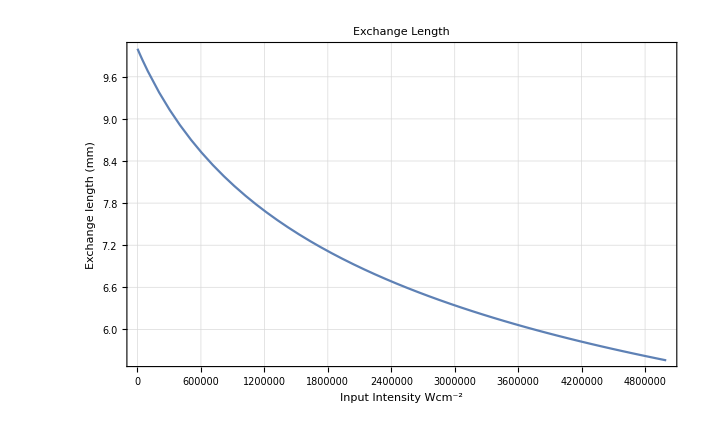

Plot::exclul: {((1-√(1+Times[«2»])+7.03867×10^-7 Irrad) Sin[Phase]^2)/(1+√(1+Times[«2»])+7.03867×10^-7 Irrad)-1,(1-(1.42072×10^6 (-1+√Plus[«2»]))/Irrad) Sin[Phase]^2-1,Cos[Phase]-0,(1+1.40773×10^-6 Irrad)-0,(1+√(1+1.40773×10^-6 Irrad)+7.03867×10^-7 Irrad)-0,Irrad-0,(1+√(1+1.40773×10^-6 Irrad)+7.03867×10^-7 Irrad)-0,1.40773×10^-6 Im[Irrad]-0,Im[√(1+1.40773×10^-6 Irrad)+7.03867×10^-7 Irrad]-0} must be a list of equalities or real-valued functions.

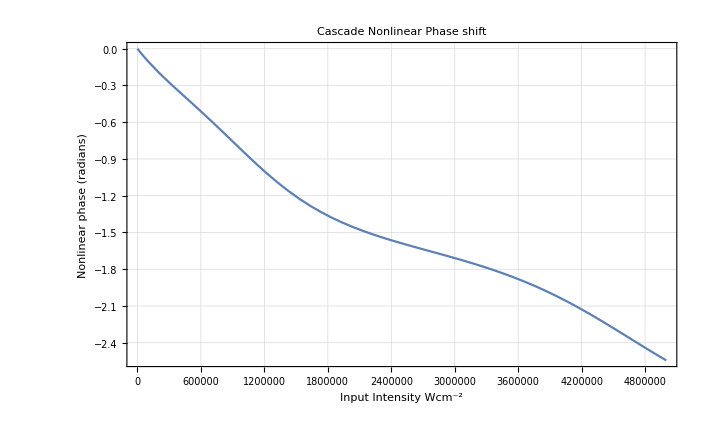

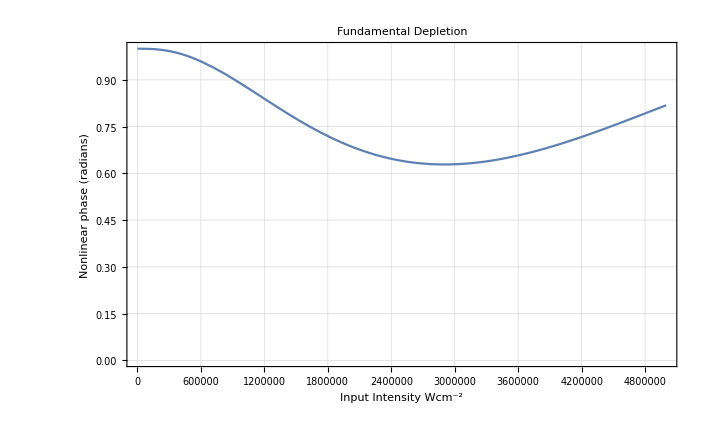

```mathematica
(*This section calculates and plots the exchange length, fundamental depletion and nonlinear phase shift - the equation numbers are refering to "An All-Optical Switch Employing the Cascaded 2nd-Order Nonlinear Effect," IEEE Journal of Quantum Electronics,vol.29,pp.2650-2654,Oct 1993http://dx.doi.org/10.1109/3.250387*)

EField:=Sqrt[(Irrad×10^4)*377/nω]; (*Electric Field using the characteristic impedance of free space*)
(*now work out parameters in the paper*)
Γ:=k*deff*EField/(Sqrt[nω*n2ω]); (*Equation 5 in paper*)
Δk:=miss*Pi/len;(*DeltaKL product set to Miss*Pi*)
Eppi:=(2*Γ/Δk)^2; (*Equation (6)*)
R1Sq:=(1/(2*Eppi))*(-1-Sqrt[1+4*Eppi]);(*Equation 12a*)
R2Sq:=(1/(2*Eppi))*(-1+Sqrt[1+4*Eppi]); (*Equation 12b*)
Z:=(Δk*len/(2*Sqrt[2.0]))*Sqrt[1+2*Eppi+Sqrt[1+4*Eppi]];(*Equation 14a*)
Deplet:=1-R2Sq;
m:=(1+2*Eppi-Sqrt[1+4*Eppi])/(1+2*Eppi+Sqrt[1+4*Eppi]);(*Equation 14b*)alpha:=Sqrt[1+2*Eppi+Sqrt[1+4*Eppi]]/Sqrt[2.0];(*equation 18*)
zpp:=4*Sqrt[2.0]/Sqrt[1+2*Eppi+Sqrt[1+4*Eppi]]/Δk; (*equation 15*)
zp:=zpp*EllipticK[m]; (*equation 15*)
DepLen2:=2*len/zp; (*Needed to sort out correct value of ArcSin*)
IntLen:=Floor[DepLen2];(*Needed to sort out correct value of ArcSin*)
Phase:=IntLen*Pi+2*Abs[ArcSin[JacobiSN[Z,m]]]/;EvenQ[IntLen]; (*equation 17*)
Phase:=IntLen*Pi+2*Abs[(Abs[ArcSin[JacobiSN[Z,m]]]-Pi/2)]/;OddQ[IntLen];(*equation 17 plus need to sort out correct principal value of ArcSin*)
Thetall=-EllipticPi[Deplet,Phase,m]/alpha;(*Equation 16*)
thetanl:=(Thetall+ Δk*len);(*Equation 19*)
(*Now Calculate Remaining Fundamental*)
RSq=1-(1-R2Sq)*(JacobiSN[Z,m])^2;(*equation 13*)
Padding:=10
Plotzp=Plot[{Abs[zp]*10^3},{Irrad,0,50×10^5},PlotRange->Automatic,Frame->True,PlotLabel->"(a) Exchange Length",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]},FrameLabel->{"Input Intensity Wcm^-2","Exchange length (mm)"},FrameStyle->Thick,ImagePadding->50];
PlotDeplete=Plot[{RSq},{Irrad,0,50×10^5},PlotRange->{0,1},Frame->True,PlotLabel->"(b) Fundamental Depletion",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]},FrameLabel->{"Input Intensity Wcm^-2","Nonlinear phase (radians)"},FrameStyle->Thick,PlotRange->{0,1},ImagePadding->50];
Plotthetanl=Plot[{thetanl},{Irrad,0,50×10^5},PlotRange->Automatic,Frame->True,PlotLabel->" (c) Cascade Nonlinear Phase shift",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",18,GrayLevel[0]},FrameLabel->{"Input Intensity Wcm^-2","Nonlinear phase (radians)"},FrameStyle->Thick,ImagePadding->50];

Plot[{Abs[zp]*10^3},{Irrad,0,50×10^5},
	PlotRange->Automatic,Frame->True,PlotLabel->"Exchange Length",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{"Input Intensity Wcm^-2","Exchange length (mm)"},FrameStyle->Thick]
Plot[{thetanl},{Irrad,0,50×10^5},
	PlotRange->Automatic,Frame->True,PlotLabel->"Cascade Nonlinear Phase shift",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{"Input Intensity Wcm^-2","Nonlinear phase (radians)"},FrameStyle->Thick]
Plot[{RSq},{Irrad,0,50×10^5},
	PlotRange->{0,1},Frame->True,PlotLabel->"Fundamental Depletion",AxesStyle->Thin,GridLines->Automatic,LabelStyle->{FontFamily->"Times New Roman",24,GrayLevel[0]},FrameLabel->{"Input Intensity Wcm^-2","Nonlinear phase (radians)"},FrameStyle->Thick]
```

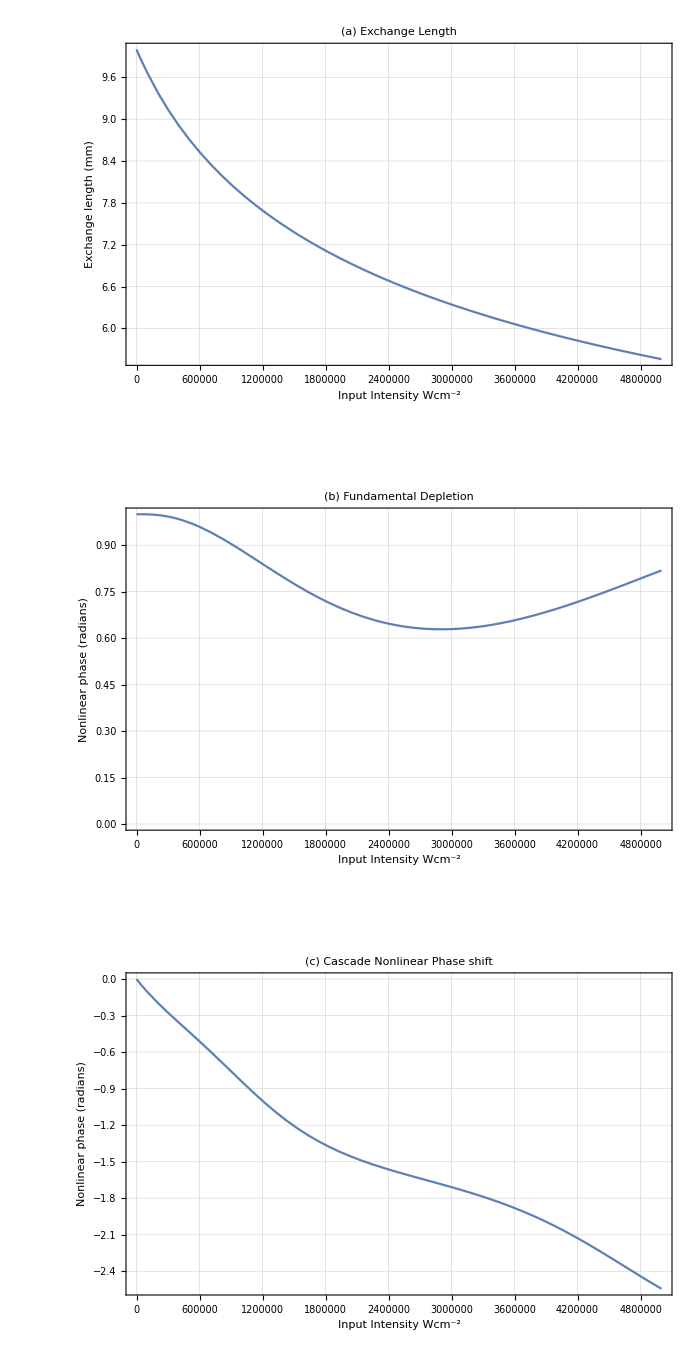

```mathematica
GraphicsGrid[{{Plotzp},{PlotDeplete},{Plotthetanl}},ImageSize->700,Frame->True]
```